```mathematica
MemoryInUse[]
Clear["Global`*"]
Unprotect[In,Out];
Clear[In,Out];
Protect[In, Out];
MemoryInUse[]
SetOptions[$FrontEnd,"ClearEvaluationQueueOnKernelQuit"->False];
```

150390800

111441120

To  understand  the  dynamics  of  strategies  in  the  game, we  use  replicator  dynamics . The  idea  stems  from  the  evolutionary  principle  that  assumes  beneficial  strategies  spread  quickly  in  a  population  while  the  least  beneficial  are  eliminated  quickly . Fitness  is  calculated  using  the  average  payoff . Our  model  assumes  infinite  population  size
Using  the  payoff  matrix = (a, b, c, d)  in  a  population  (strategy1, strategy2)
Frequency  of  strategy1 = x, strategy2 = 1 - x
s1 = (a (x) + b (1 - x))
s2 = (a (x) + b (1 - x))
x = x[Fitness_x - (xFitness_x)]

Our  model  assumes  a  finite  population  size  N?Using  the  payoff  matrix = (a, b, c, d)  in  a  population  (strategy1, strategy2)
Frequency  of  strategy1 = x, strategy2 = N - x
s1 = (a (x - 1) + b (N - x))/N - 1
s2 = (a (x) + b (N - x - 1))/N - 1

## Initialize section

#### The following functions are used for all the rounds and strategy conditions

```mathematica
(*SET GENERAL FONT SIZE*)
genfont={Black,"Helvetica",26};
genfont2={Black,"Helvetica",22};
genfont3={Black,"Helvetica",21};

(*tart60=Show[Import[NotebookDirectory[]<>"Untitled_Artwork 19.png"],ImageSize->60];*)
```

```mathematica
tart60=-Graphics-;
```

```mathematica
(*determines the table heading from strategy list*)
getheadings=.
getheadings[pom_,headingI_]:=Transpose[Join[{Join[{""},headingI[[2]]]},Transpose[Join[{headingI[[1]]},pom]]]]

(*formats the payoff matrix fo it fits in the table*)
payoffMatrixFormat=.
payoffMatrixFormat[pom_,gfont_,sp_:{2,2},is_:400]:=GraphicsGrid[(pom),Dividers->{{2->Directive[{Black,Thick}]},{2->Directive[{Black,Thick}]}},(*ItemSize->1,*)(*ItemStyle->{Black,"Helvetica",18},*)Spacings->sp,ImagePadding->{{10,10},{30,30}},BaseStyle->gfont,ImageSize->is](*]*)
```

### payoff matrix

The following is the  function that calculates the payoff matrix for two players depending on the strategy space

```mathematica
Clear[payoffCalNRound] (*conditional and unconditional payoffs *)
payoffCalNRound[player1_, player2_,costofkilling_,opt_:{0,0}]:=Block[{pot=0,tokill=-1,frst1=0,frst2=0,sec1=0,sec2=0,cellslost=0},
frst1=player1[[1]]/._?Negative->0;
frst2=player2[[1]]/._?Negative->0;
pot=frst1+frst2;
Which[(opt[[1]]==1)&&(Length[player1]>1), (*conditional opt[[1]]=1*)
If[pot>player1[[3]],sec1=player1[[2,2]];,sec1=player1[[2,1]];];
If[pot>player2[[3]],sec2=player2[[2,2]];,sec2=player2[[2,1]];];
,
(opt[[1]]==0)&&(Length[player1]>1),
(*unconditional opt[[1]]=0*)
sec1=player1[[2]];
sec2=player2[[2]];
];

(*Print[pot,sec1,sec2];*)
If[Length[player1]>1,
Which[(opt[[2]]==0 ),tokill=Total[Select[{sec1,sec2},#<0&]];

cellslost=If[pot<=0,0.,Min[{Total[Table[If[(pot-i)<=0,0.,N[(frst1/(pot-i))]],{i,0,Abs[Total[tokill]]-1}]],1.*frst1}]]
,
((opt[[2]]==1 )(*NotME*)&&(player1==player2)),tokill=-1; cellslost=0.;,
((opt[[2]]==1 )(*NotME*)&&(player1 != player2)),tokill=Select[{sec2},#<0.&];
If[frst1<sec2,cellslost=frst1,cellslost=sec2];,
((opt[[2]]==2 )(*NotMENOWStrategy*)&&(player1[[2]]==player2[[2]])),tokill=-1 ;cellslost=0.;,
((opt[[2]]==2 )(*NotMENOWStrategy*)&&(player1[[2]]!= player2[[2]])),
tokill=Select[{sec2},#<0.&];
If[frst1<sec2,cellslost=frst1,cellslost=sec2];,
((opt[[2]]==3 )(*NotMENOWAction*)&&(sec1==sec2)),tokill=-1;cellslost=0.;,
((opt[[2]]==3 )(*NotMENOWAction*)&&(sec1!=sec2)),tokill=Select[{sec2},#<0.&];
If[frst1<sec2,cellslost=frst1,cellslost=sec2];,
opt[[2]]==4 (*killUpToNOw*),tokill=Select[{sec1,sec2},#<0.&];
(*this scenario assumes that half of the time player1 will go first in round two and the new cell can be killed*)
cellslost=(If[((pot+(sec1/._?Negative->0))<=0 )|| (tokill>= 0),0.,Min[{Total[Table[If[(pot+(sec1/._?Negative->0)-i)<=0,0.,N[(frst1+(sec1/._?Negative->0))/(pot+(sec1/._?Negative->0)-i)]],{i,0.,Abs[Total[tokill]]-1.}]],1.*frst1}]]+
If[((pot+(sec2/._?Negative->0))<=0 )|| (tokill>= 0),0.,Min[{Total[Table[If[(pot+(sec2/._?Negative->0)-i)<=0,0.,N[(frst1/(pot+(sec2/._?Negative->0)-i))]],{i,0.,Abs[Total[tokill]]-1.}]],1.*frst1}]])/2.;

];
];(*if two rounds*)

(*alternative R1 games that are sequential*)
If[((opt[[2]]==5 )&&(Length[player1]<2)),
If[player2[[1]]<0,cellslost=0.5];
If[player1[[1]]<0,sec1=-1];
];
If[((opt[[2]]==6 )&&(Length[player1]<2)),
If[(player2[[1]]<0)&&(player1[[1]]>0),cellslost=0.5];
If[player1[[1]]<0,sec1=-1];
];
Total[{frst1,(sec1/._?Negative->0),If[sec1<0,-costofkilling,0],-cellslost}](*total*)


]
```

### stream functions

```mathematica
pMprob=.
pMprob[pH_, totalcell_,ct_,prob_]:=Table[(*Print[totalcell[[i,j]]==ct];*)If[totalcell[[i,j]]==ct,pH[[i,j]],pH[[i,j]](1-prob)],{i,1,Length[pH]},{j,1,Length[pH]}]
```

```mathematica
Off[Interpolation::indp]
(*important many player fn...group size can change*)
fM=.
fM[fx_,groupS_]:=Flatten[Table[(groupS!/(Ax!Bx!(groupS-Ax-Bx)!))If[((fx[[1]]==0)&&Ax==0),1,fx[[1]]^Ax]If[((fx[[2]]==0)&&(Bx==0)),1, fx[[2]]^Bx ]If[((fx[[3]]==0)&&((Bx==0)&&(Ax==0))||(Bx+Ax==groupS)),1,fx[[3]]^(groupS-Ax-Bx)],{Ax,groupS,0,-1},{Bx,groupS-Ax,0,-1}],1];

indPayoff=.
indPayoff[fx_,groupS_,payoffM_]:=Total[fM[fx,groupS]#]&/@ payoffM;
(*repliator function*)
repFn=.
repFn[fx_,groupS_,payoffM_]:=fx (indPayoff[fx,groupS,payoffM]-(indPayoff[fx,groupS,payoffM].fx));
Speed=.;
Speed[fx_,groupS_,payoffM_]:=Sqrt[(Total[(repFn[fx,groupS,payoffM])^(2)])^(1/3)];
Clear[funStream]
(*
mtf,pMprob[allp,cellTarget,#[[1]],#[[2]]],2,#[[1]],#[[2]],vl,is,ip
	allplayers_ => strategy matrix
payOffM_ => matrix calculated from pMprob
M_ ->method
ct_=>cell target
prob_=>probability,
loc_ list that tell the graph where to place things{{{-0.3,1.1},{-0.1,1.14}},{0.51,0.899},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.18,0.85}},
is_:480 =>image size
,ip_:Automatic => image Padding
*)
funStream[allplayers_,payOffM_,M_,ct_,prob_,loc_:{{{-0.3,1.1},{-0.1,1.14}},{0.51,0.899},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.18,0.85}},is_:480,ip_:Automatic,tarty_:tart60]:=Block[{tri,baryC,TA, maxS,t,ls},(*creating a matrix for many players*)
tri=Partition[{{0,0},{1/2,Sqrt[3]/2},{1,0}},2,1,-1];

(*creating barycentric coordinate system*)
baryC=Join[{{0,0,1},{1,0,0},{0,1,0}},Flatten[Flatten[Table[If[a+b≤1,{Total[({{0,0,1},{1,0,0},{0,1,0}}{a,b,1-b-a})]},{}],{a,0,1,0.05},{b,0,1,0.05}],{1,3}],1]];

(*this is the transformation matrix*)
TA={{.5,0,1},{(√3)/2,0,0},{0,0,1}};

(***COLOR FUNCTION*********code is modified from the dynamo.nb files*********)

btwf=.;
maxS=Max[Speed[#,M-1,payOffM]&/@baryC];
btwf[Ψ_,minAttained_:0,maxAttained_:maxS]:=Max[0,Min[(Ψ-minAttained)/(maxAttained-minAttained),1]] ;

colFun=.;
colFun[Ψ_]:=Hue[ Which[btwf[Ψ]≤1/2,2/5 btwf[Ψ],1/2<btwf[Ψ]≤2/3, 6/5 btwf[Ψ]-2/5,2/3<btwf[Ψ],3/4 btwf[Ψ]-1/10]];

t=Graphics[{Black,Line/@tri}];
(*plots the stream*)

ls=ListStreamDensityPlot[
Table[{Take[TA.baryC⟦i⟧,2],{Take[TA.repFn[baryC⟦i⟧,M-1,payOffM],2],Speed[baryC[[i]],M-1,payOffM]}},
{i,Dimensions[baryC]⟦1⟧}],(*VectorPoints->8,VectorScale->{0.02,Automatic,None},VectorStyle->{Black,Arrowheads[0.025]},*)
StreamStyle->{Black,Arrowheads[0.02]},StreamScale->{.5,250,0.5},StreamPoints->{100,0.03,.1},StreamColorFunction->Black,Frame->False,ColorFunctionScaling->False ,ColorFunction->(Lighter[#,0.72]&/@{RGBColor[0.300725, 0.680491, 0.901701],RGBColor[0.300725, 0.680491, 0.901701],(*RGBColor[0.945344, 0.7896250000000001, 0.482689],*)RGBColor[0.945344, 0.7896250000000001, 0.482689],RGBColor[0.945344, 0.7896250000000001, 0.482689],RGBColor[0.945344, 0.7896250000000001, 0.482689](*,RGBColor[0.7389030000000001, 0.424989, 0.675772],RGBColor[0.604318, 0.51771, 0.780231]*)}),(*ColorFunction->(colFun[#1]&),*)
DisplayFunction->Identity,PlotRange->loc[[1]],

Epilog->{Text[#[[1]],#[[2]]]&/@{{Style[(*oString[*)allplayers[[1]], genfont],loc[[2]]},{(*"SO="<>*)Style[allplayers[[2]], genfont],loc[[3]]},
{Style[allplayers[[3]],genfont],loc[[4]]}},
Inset[TableForm[{{tarty, Style["target = "<>ToString[ct]<>If[ct==1," cell"," cells"],genfont]}},TableSpacing->{-10,-10},TableAlignments->{Center,Center}],Scaled[loc[[5]]],Left],
Text[Style["p = "<>ToString[1-prob],genfont],Scaled[loc[[6]]],Left]},ImagePadding->ip,PlotRangePadding->True,RegionFunction->Function[{x,y,vx,vy,n},(√3 x) >   y  &&(y <  -√3 (-1+x))&&(y ≤   √3 /2)&&(y >=   0)](*,PerformanceGoal->"Quality"*)];
Show[ls,t,ImageSize->is,ImagePadding->ip]]
```

```mathematica
Off[Interpolation::indp]
```

```mathematica
Clear[getStrategyList]
getStrategyList[strlist_,rounds_,cond_:{0,0}]:=Block[{allplayers=Tuples[strlist,rounds],allpcont2,allpcont},
allpcont2=allplayers;
(*unconditonal game options*)
(*cond={0,0};*) (*(0,5},{0,6}*)
(*conditonal game options*)
(*cond={1,0};*) (*or cond={1,0,-1} to include Ks in the first round*)

(*removes killers in the first round to reduce strat space unless specifies*)
If[(rounds>1.)&&(cond[[1]]==0),
If[Length[cond]==3,allpcont2[[All,1]]=allpcont2[[All,1]],
allpcont2[[All,1]]=allpcont2[[All,1]]/._?Negative->0;];
];
If[cond[[1]]==1,
allpcont=Tuples[allplayers,rounds];
allpcont2=allpcont;
If[rounds>1.,
If[Length[cond]==3,allpcont2[[All,1]]=allpcont2[[All,1,1]],
allpcont2[[All,1]]=allpcont2[[All,1,1]]/._?Negative->0;];(*no negative in the first spot*)
allpcont2[[All,2,1]]=allpcont2[[All,2,1]]/._?Negative->0;(*no negative in the first condition*)
allpcont2[[All,2,2]]=allpcont2[[All,2,2]]/._?Positive->-1;(*only negative in the secod condition*)
];
allpcont2=Union[allpcont2]; (*remove duplicates*)
allpcont2=Flatten[Map[Function[dummy,Join[dummy,{#}]&/@Range[0,Max[strlist]*rounds,1]],allpcont2],1];
,
allpcont2=Union[allpcont2];
];
Union[allpcont2]
]
```

```mathematica
replaceList={1->"C",-1->"K",0->"N",2->"2C"}
```

{1→C,-1→K,0→N,2→2C}

```mathematica
matstrat=.
matstrat[strata_,gfont_:{Black,"Helvetica",16}]:=If[Length[strata]<2,Style[MatrixForm[strata],gfont],Style[MatrixForm[Transpose[strata],TableDirections->Row],gfont]]
```

```mathematica
colapseStratFn=.
colapseStratFn[strata_]:=Which[strata[[3]]==strata[[1]],If[strata[[2,1]]==strata[[2,2]],{strata[[1]],strata[[2,1]]},{strata[[1]],#}&/@strata[[2]]],strata[[3]]>strata[[1]],{strata[[1]],strata[[2,1]]},strata[[3]]<strata[[1]],{strata[[1]],strata[[2,2]]}]
```

```mathematica
(*allplayers=> matrix of player strategies
,costofkilling,
cond {0,0} unconditional, {1,0} are conditional
replaceList -> {1->"C",-1->"K",0->"N",2->"2C"}
targetrisk => { target,probability risk}->{{1,0.95},{2,0.95},{3,0.95}},
genf_=> font to use genfont3,
 matsize-> matrix image size
vl_-> location of labels in figure
is -> image size
ip->image padding
*)
(*outputs just the matrix then the stream plots for each risk and target*)
getStreamPlot=.
getStreamPlot[allplayers_,costofkilling_,cond_,replaceList_,targetrisk_:{{1,0.95},{2,0.95},{3,0.95}},genf_:genfont3, matsize_:400,vl_:{{{-0.3,1.1},{-0.1,1.14}},{0.51,0.9199},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.18,0.85}},is_:480,ip_:Automatic,tarty_:tart60]:=Block[{allpcont2=allplayers,mtf,cellTarget,allp},
allp=Table[payoffCalNRound[i,j,costofkilling,cond],{i,allpcont2},{j,allpcont2}];
If[cond[[1]]==1,mtf=matstrat[#,genf]&/@((colapseStratFn[#]&/@allpcont2)/.replaceList),
mtf=matstrat[#,genf]&/@(allpcont2/.replaceList)];
cellTarget=N[Table[payoffCalNRound[i,j,costofkilling,cond]+payoffCalNRound[j,i,costofkilling,cond],{i,allpcont2},{j,allpcont2}]];
{payoffMatrixFormat[getheadings[(allp/.{0.->0,1.->1,2.->2,3.->3,4.->4})*C*"P",{mtf,mtf}],genf,{3,1},matsize]/.{ 0.->0,1.->1},Map[funStream[mtf,pMprob[allp,cellTarget,#[[1]],#[[2]]],2,#[[1]],#[[2]],vl,is,ip,tarty]&,targetrisk],Map[ payoffMatrixFormat[getheadings[pMprob[allp,cellTarget,#[[1]],#[[2]]],{mtf,mtf}],genf,{2,1},matsize]&,targetrisk]/.{ 0.->0,1.->1}}
]
```

```mathematica
(*allplayers=> matrix of player strategies
,costofkilling,
cond {0,0} unconditional, {1,0} are conditional
replaceList -> {1->"C",-1->"K",0->"N",2->"2C"}
targetrisk => { target,probability risk}->{{1,0.95},{2,0.95},{3,0.95}},
genf_=> font to use genfont3,
 matsize-> matrix image size
vl_-> location of labels in figure
is -> image size
ip->image padding
*)
(*outputs just the matrix*)
getStreamMatt=.
getStreamMatt[allplayers_,costofkilling_,cond_,replaceList_,targetrisk_:{{1,0.95},{2,0.95},{3,0.95}},genf_:genfont3, matsize_:400,vl_:{{{-0.3,1.1},{-0.1,1.14}},{0.51,0.9199},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.18,0.85}},is_:480,ip_:Automatic]:=Block[{allpcont2=allplayers,mtf,cellTarget,allp},
allp=Table[payoffCalNRound[i,j,costofkilling,cond],{i,allpcont2},{j,allpcont2}];
(*Print[allp];*)
If[cond[[1]]==1,mtf=matstrat[#,genf]&/@((colapseStratFn[#]&/@allpcont2)/.replaceList),
mtf=matstrat[#,genf]&/@(allpcont2/.replaceList)];
cellTarget=N[Table[payoffCalNRound[i,j,costofkilling,cond]+payoffCalNRound[j,i,costofkilling,cond],{i,allpcont2},{j,allpcont2}]];
{payoffMatrixFormat[getheadings[(allp/.{0.->0,-1.->-1,1.->1,2.->2,3.->3,4.->4})*C*"P",{mtf,mtf}],genf,{3,1},matsize]/.{ 0.->0,1.->1},payoffMatrixFormat[getheadings[pMprob[allp,cellTarget,targetrisk[[1]],targetrisk[[2]]],{mtf,mtf}],genf,{3,1},matsize]/.{ 0.->0,1.->1}}
]
```

## One round

```mathematica
(*SET GENERAL FONT SIZE*)
genfont={Black,"Helvetica",32};
genfont2={Black,"Helvetica",28};
genfont3={Black,"Helvetica",30};

(*tart60=Show[Import[NotebookDirectory[]<>"Untitled_Artwork 19.png"],ImageSize->80];*)
```

```mathematica
(*SET GENERAL round 1 game information *)
tart601=Show[tart60,ImageSize->70];
vl={{{-0.3,1.1},{-0.1,1.14}},{0.51,0.9199},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.15,0.85}};is=480;
ip=Automatic;
costofkilling=0;
rounds=1;
```

#### Figure N K C

```mathematica
tart601=Show[tart60,ImageSize->70];
vl={{{-0.3,1.1},{-0.1,1.14}},{0.51,0.9199},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.15,0.85}};is=480;
ip=Automatic;
costofkilling=0;
rounds=1;cond={0,0}
strlist={-1,0,1};
allplayers=getStrategyList[strlist,rounds]
targrisk={{1,0.95},{2,0.95},{3,0.95}};
```

{0,0}

{{-1},{0},{1}}

```mathematica
r1a=getStreamPlot[allplayers,costofkilling,cond,replaceList,targrisk,genfont3,400, vl,is,ip ,tart601];
```

{0,0}

{{-1},{0},{1}}

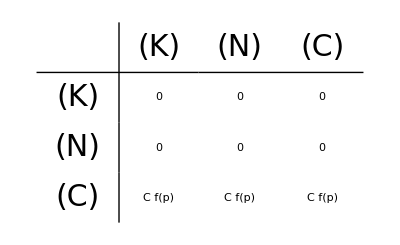
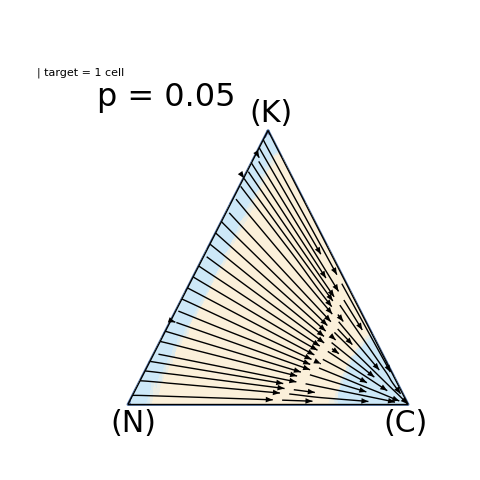
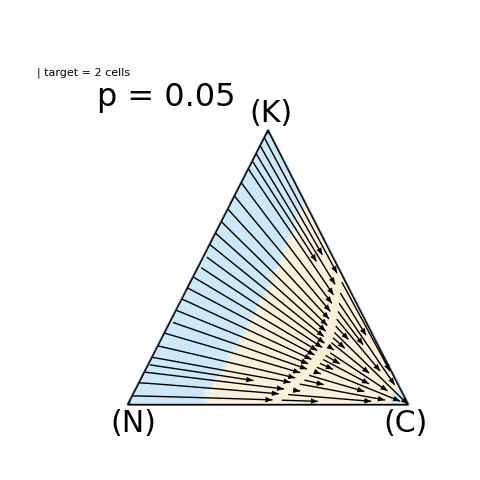
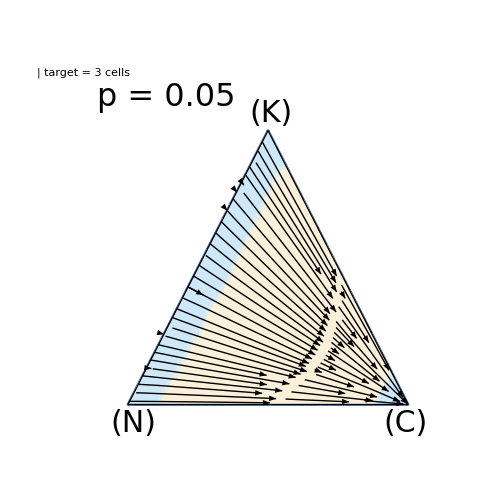
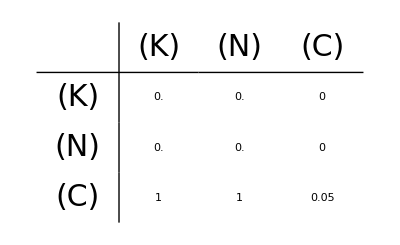
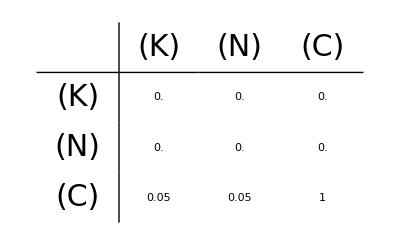
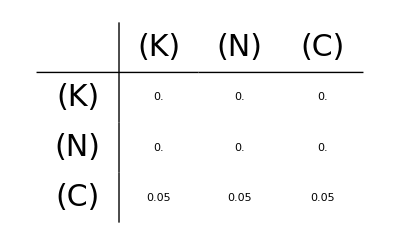

```mathematica
r1a
```

#### Figure K C 2C

```mathematica
vl={{{-0.3,1.1},{-0.1,1.14}},{0.51,0.9199},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.15,0.85}};is=480;
ip=Automatic;
costofkilling=0;
rounds=1;
```

```mathematica
cond={0,0}
rounds=1
strlist={-1,0,1,2};
allplayers=getStrategyList[strlist,rounds];
allpcont2=allplayers[[{1,3,4}]]; (*K C 2C*)
r1b=getStreamPlot[allplayers[[{1,3,4}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}},genfont3,500,vl,is,ip ,tart601];
r1b4=getStreamPlot[allplayers[[{1,3,4}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}},genfont3,470,vl,is,ip ,tart601];
```

{0,0}

1

#### Figure 1d

```mathematica
r1r=TableForm[{r1a[[3,1]],r1a[[2,2]]},TableDirections->Row,TableAlignments->Top,TableSpacing->0];
```

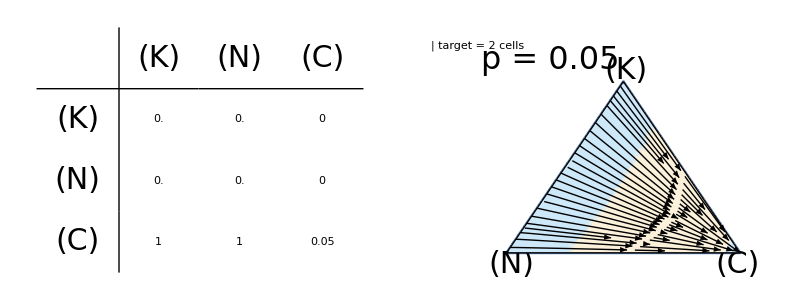

```mathematica
r1r
```

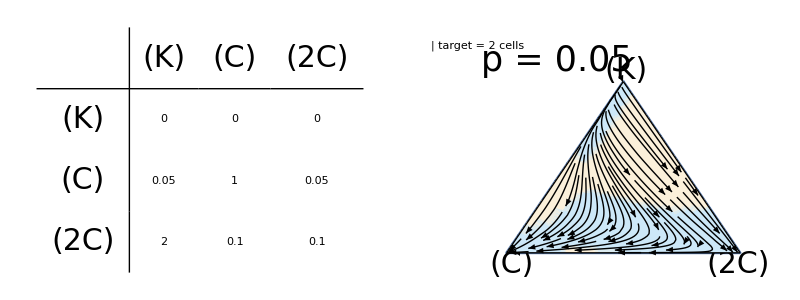

```mathematica
fig1d=TableForm[{Show[r1b[[3,2]]/. 0.->0,ImageSize->400],r1b[[2,2]]},TableDirections->Row,TableAlignments->Top,TableSpacing->1]
```

```mathematica
Export[NotebookDirectory[]<>"streamR1"<>ToString[{2,0.95}]<>"2026survivalrow-F1d.png",fig1d]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/streamR1{2, 0.95}2026survivalrow-F1d.png

#### Sup Figure 1

```mathematica
sup1=TableForm[{TableForm[{Show[#,ImageSize->400]&/@(r1a[[3]]/. 0.->0),r1a[[2]]},TableSpacing->{0,6,7}, TableAlignments->Center],TableForm[{Show[#,ImageSize->400]&/@(r1b[[3]]/. 0.->0),r1b[[2]]},TableSpacing->{0,6,7}, TableAlignments->Center]},TableDirections->Column,TableSpacing->10];
```

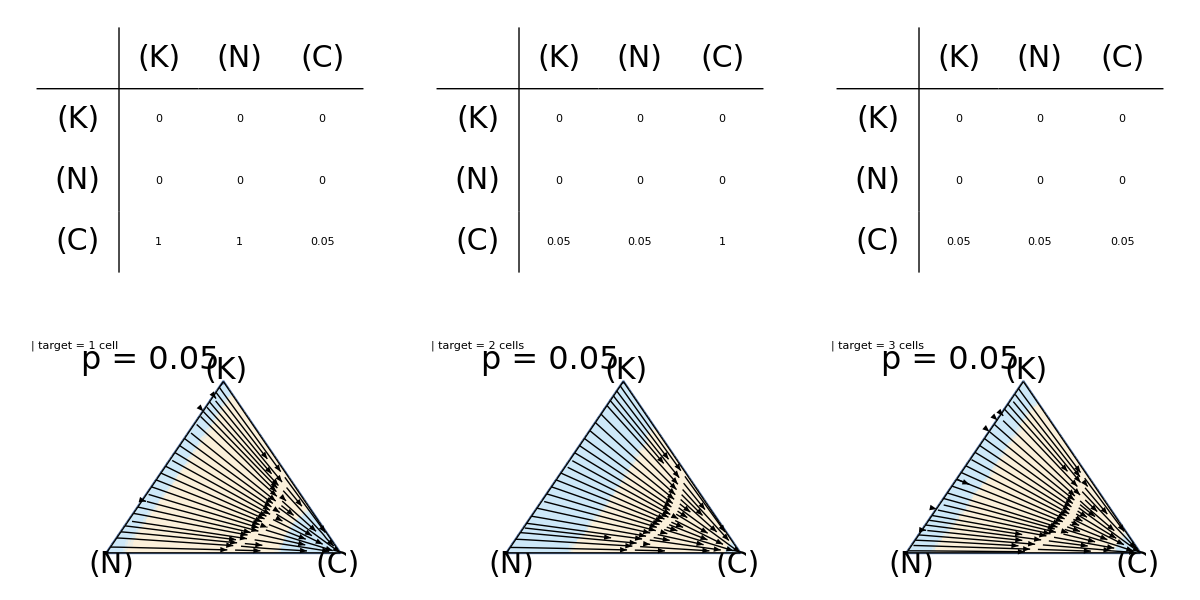
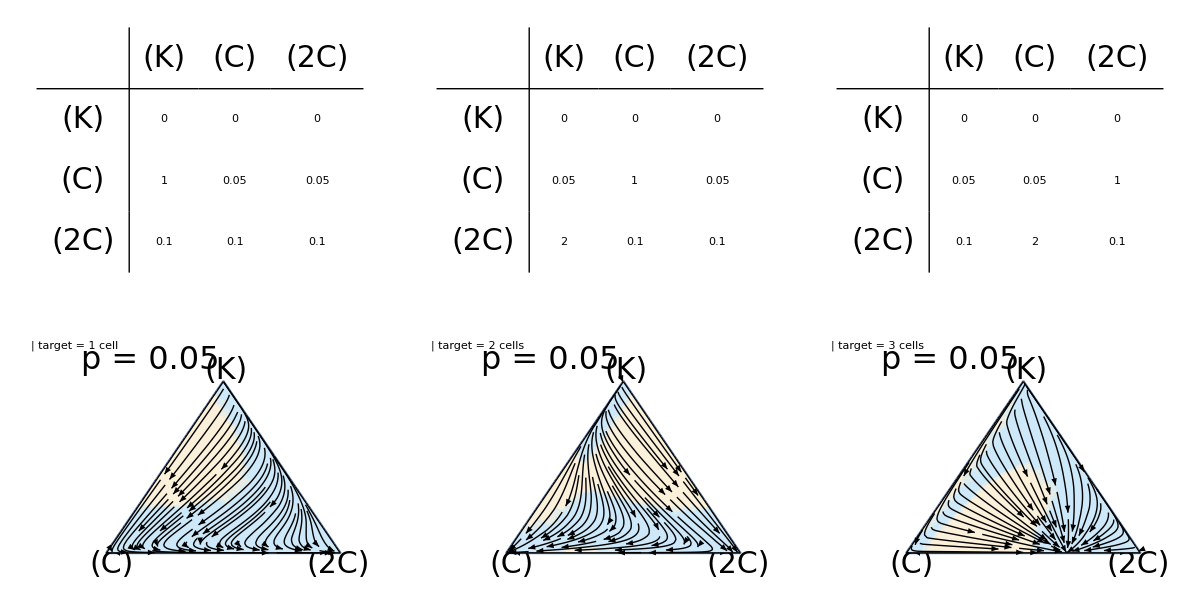

```mathematica
sup1
```

```mathematica
Export[NotebookDirectory[]<>"streamR1"<>ToString[{1-3,0.95}]<>"-S1-2026survival.png",sup1,ImageSize->2000,ImageResolution->300(*,ImageSize->650*)(*,ImagePadding->{{10, 10}, {30, 30}}*)]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/streamR1{-2, 0.95}-S1-2026survival.png

#### Sup Figure 2a matrix

```mathematica
cond={0,6};
strlist={1,0,-1};
allplayers=getStrategyList[strlist,rounds];
(*generates the matrix for S2*)
r1a05=getStreamMatt[allplayers,costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}},genfont3,550];
```

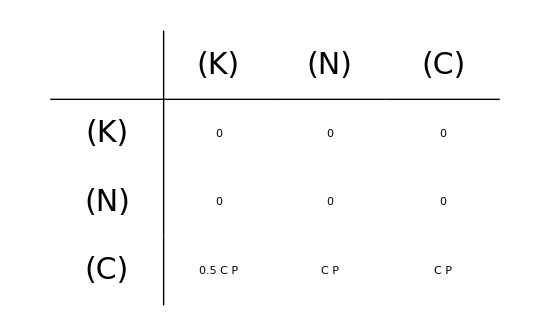
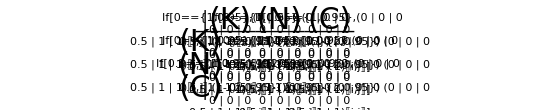

```mathematica
r1a05
```

```mathematica
Export[NotebookDirectory[]<>"streamR1"<>ToString[{0,5}]<>"-S2-"<>ToString[cond]<>"survival05.png",r1a05[[1]]]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/streamR1{0, 5}-S2-{0, 6}survival05.png

## Two Rounds

```mathematica
(*SET GENERAL FONT SIZE*)
genfont={Black,"Helvetica",35};
genfont2={Black,"Helvetica",28};
genfont3={Black,"Helvetica",30};
```

```mathematica
costofkilling=0;
cond={0,0};
rounds=2;
strlist={-1,0,1};
(*SET GENERAL round 1 game information *)
tart601=Show[tart60,ImageSize->70];
vl={{{-0.3,1.1},{-0.1,1.14}},{0.51,0.9199},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.15,0.85}};is=480;
ip=Automatic;
allplayers=getStrategyList[strlist,rounds]
vg1={{{-0.3,1.15},{-0.1,1.14}},{0.51,0.899},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.18,0.85}};
vg={{{-0.3,1.15},{-0.1,1.14}},{0.51,0.899},{0.02,-0.06},{0.99,-0.06},{1.1,1.1},{1.1,1.1}};
```

{{0,-1},{0,0},{0,1},{1,-1},{1,0},{1,1}}

#### Sims

```mathematica
{{"C","K"},{"C","N"},{"C","C"}}
```

```mathematica
allplayers[[{4,5,6}]]/.replaceList
```

{{C,K},{C,N},{C,C}}

#### Figure 2b matrix

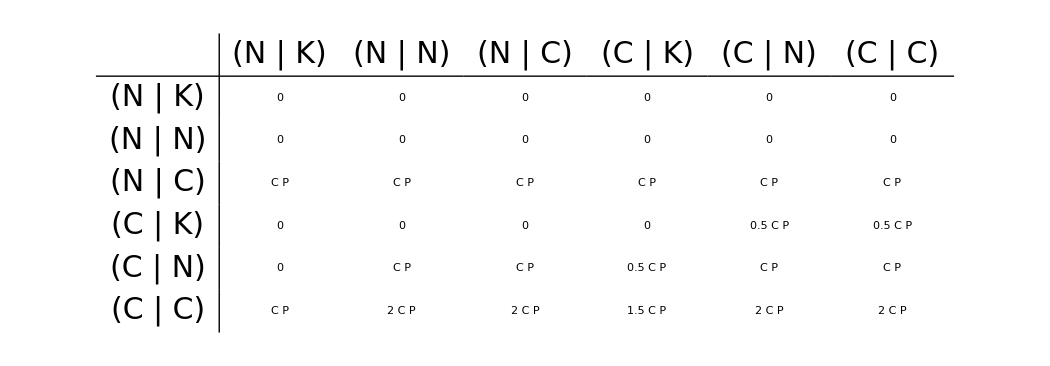
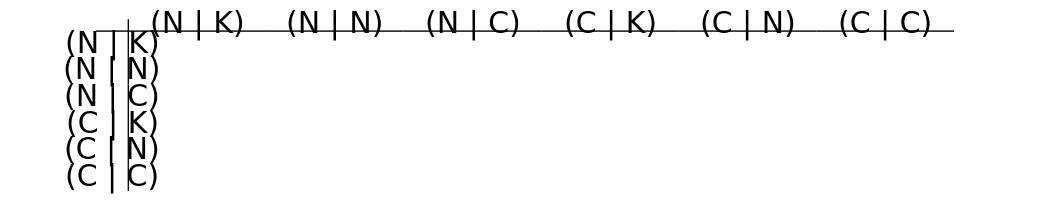

```mathematica
r2095mat=getStreamMatt[allplayers,costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}},genfont3,1050]
```

```mathematica
Export[NotebookDirectory[]<>"streamR2"<>ToString[{1-3,0.95}]<>"-2026-F2b.png",r2095mat[[1]],ImageSize->1000(*,ImagePadding->{{10, 10}, {30, 30}}*),ImageResolution->300]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/streamR2{-2, 0.95}-2026-F2b.png

#### Figure 2d and e

```mathematica
aa1a=getStreamPlot[allplayers[[{4,5,6}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95},{4,0.95}},genfont3,750,vg1,is,ip,tart601];
```

```mathematica
{{"C","K"},{"N","C"},{"C","C"}}
```

{{C,K},{N,C},{C,C}}

```mathematica
allplayers[[{4,3,6}]]/.replaceList
```

{{C,K},{N,C},{C,C}}

```mathematica
aa1b1=getStreamPlot[allplayers[[{4,3,6}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95},{4,0.95}},genfont3,750,vg1,is,ip,tart601];
(*aa1b=getStreamPlot[allplayers[[{4,3,6}]],costofkilling,cond,replaceList,{{1,0.95}(*,{2,0.95},{3,0.95},{4,0.95}*)},genfont3,750,vg]*)
```

```mathematica
{{"N","K"},{"N","C"},{"C","C"}}
```

```mathematica
allplayers[[{1,3,6}]]/.replaceList
```

{{N,K},{N,C},{C,C}}

```mathematica
aa1d1=getStreamPlot[allplayers[[{1,3,6}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95},{4,0.95}},genfont3,750,vg1,is,ip,tart601];
```

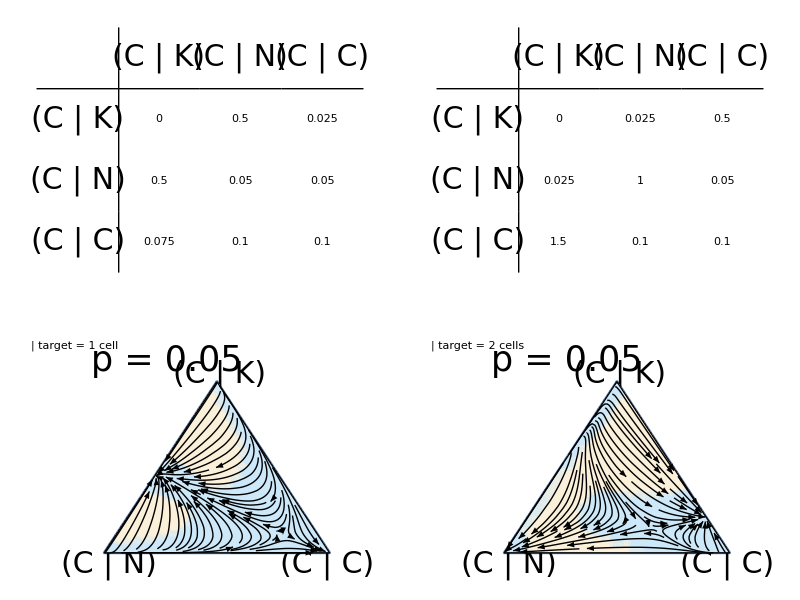
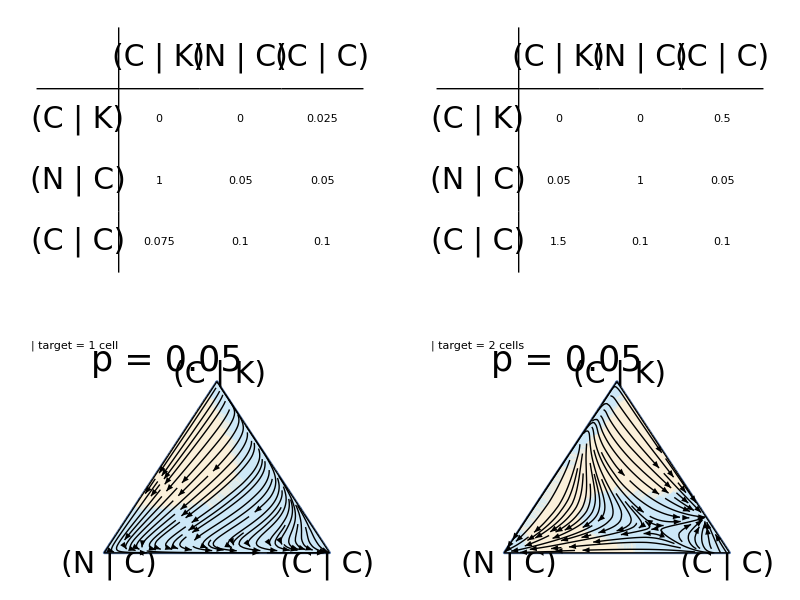
-Graphics- | -Graphics-

```mathematica
r2095ab=TableForm[{TableForm[{Show[#,ImageSize->600]&/@aa1a[[3,1;;2]]/.{ 0.->0,1.->1},aa1a[[2,1;;2]]},TableSpacing->1,TableAlignments->Center],TableForm[{Show[#,ImageSize->600]&/@aa1b1[[3,1;;2]]/.{ 0.->0,1.->1},aa1b1[[2,1;;2]]},TableSpacing->1,TableAlignments->Center]},TableDirections->Row,TableSpacing->{4,20}]
```

```mathematica
(*r2095ab=*)(*TableForm[{TableForm[{{aa1a[[1]]},TableForm[aa1a[[2,1;;2]],TableSpacing->{0, 0},TableDirections->Row]},TableSpacing->1],TableForm[{{aa1b1[[1]]},TableForm[aa1b1[[2,1;;2]],TableSpacing->{0, 0},TableDirections->Row]},TableSpacing->1]},TableDirections->Row,TableSpacing->{4,20}];*)
```

```mathematica
Export[NotebookDirectory[]<>"streamR2"<>ToString[{1-3,0.95}]<>"-2026-F2de.png",r2095ab,ImageSize->2200(*,ImagePadding->{{10, 10}, {30, 30}}*),ImageResolution->300]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/streamR2{-2, 0.95}-2026-F2de.png

#### Sup Figure 3

```mathematica
r2095=TableForm[{TableForm[{{aa1a[[1]]},TableForm[aa1a[[2]],TableSpacing->{0, 0},TableDirections->Row]},TableSpacing->-1],TableForm[{{aa1b1[[1]]},TableForm[aa1b1[[2]],TableSpacing->{0, 0},TableDirections->Row]},TableSpacing->-1],(*TableForm[{{aa1c[[1]]},TableForm[aa1c[[2]],TableSpacing->{0, 0},TableDirections->Row]},TableSpacing->-15],*)TableForm[{{aa1d1[[1]]},TableForm[aa1d1[[2]],TableSpacing->{0, 0},TableDirections->Row]},TableSpacing->-1]},TableDirections->Column,TableSpacing->8];
```

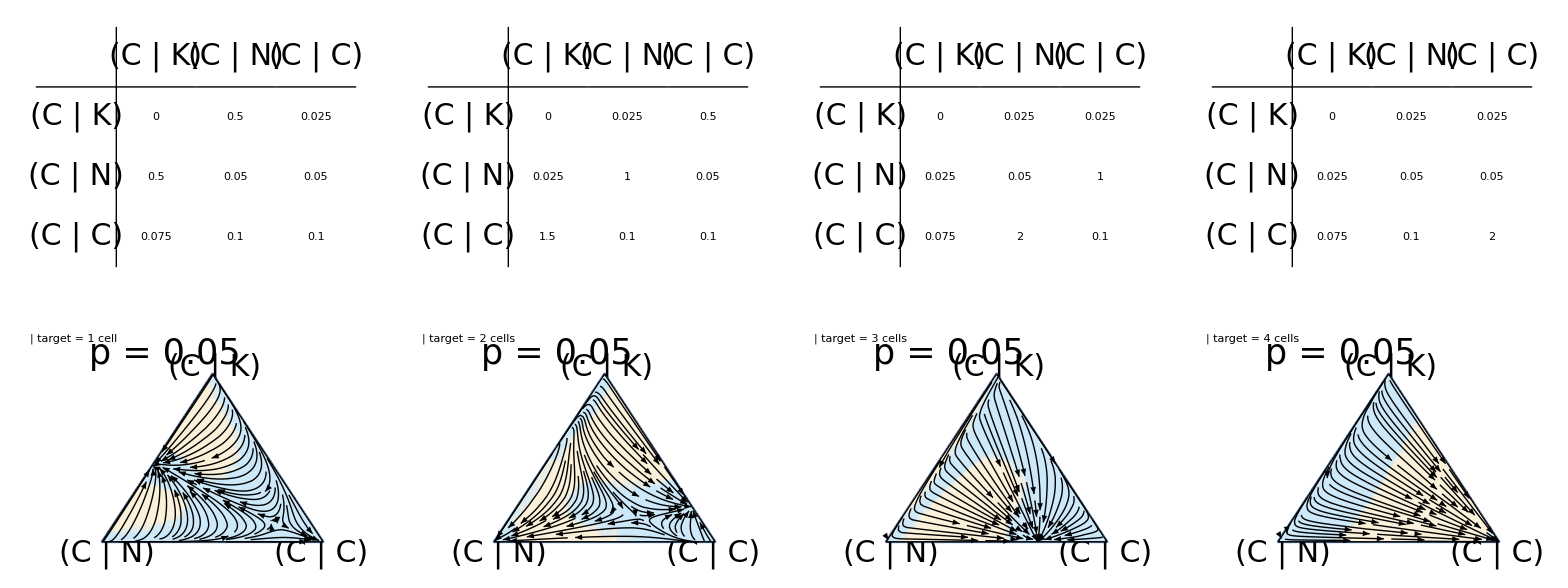
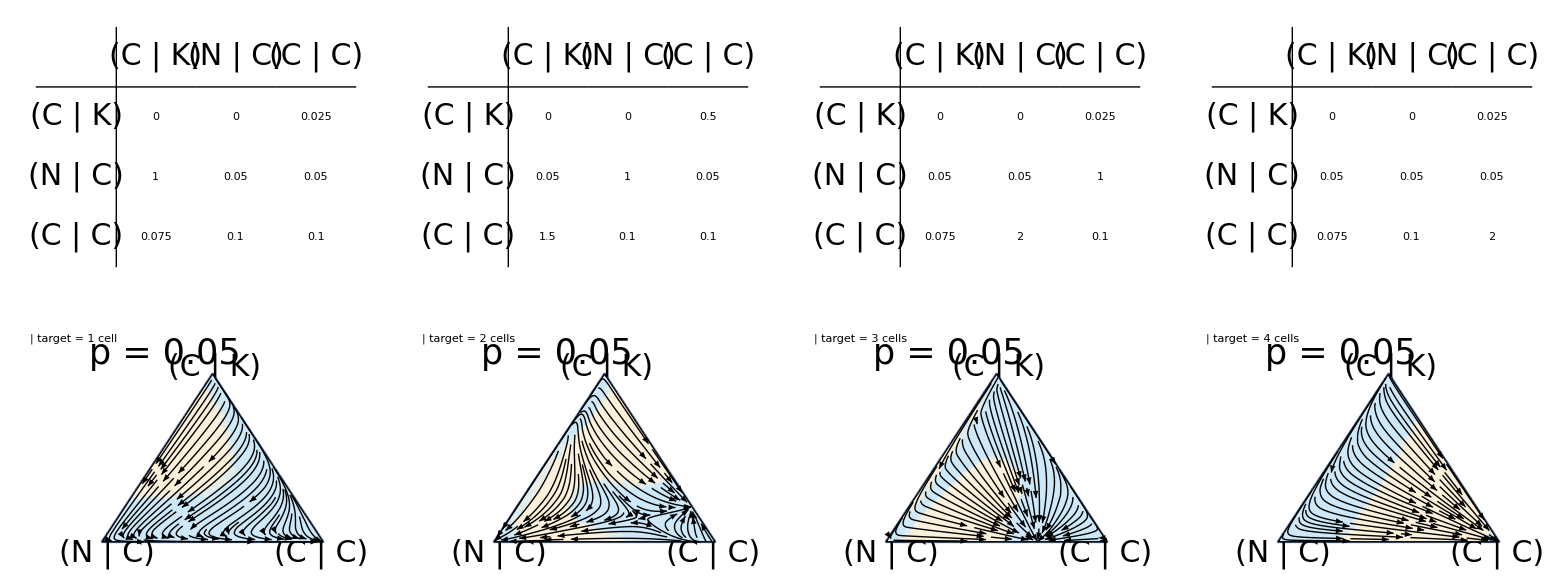
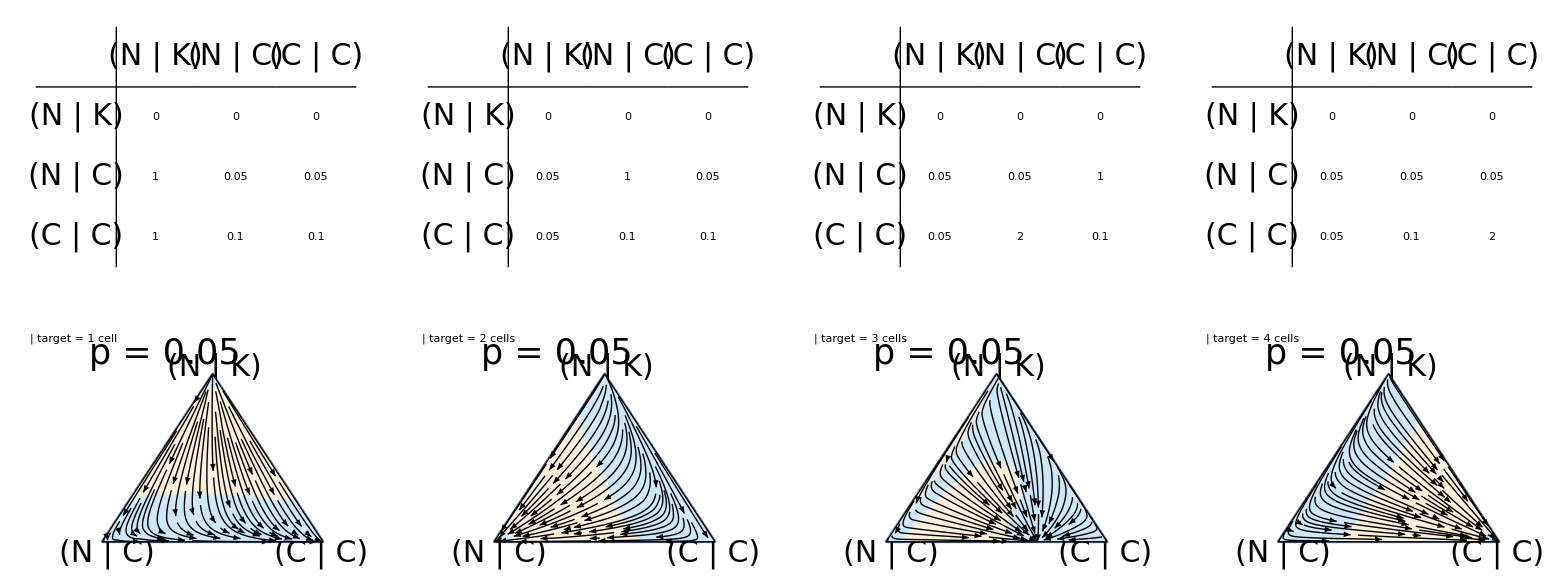

```mathematica
r2095=TableForm[{TableForm[{Show[#,ImageSize->560]&/@aa1a[[3]]/.{ 0.->0,1.->1},aa1a[[2]]},TableSpacing->-1,TableDirections->Column,TableAlignments->Center],TableForm[{Show[#,ImageSize->560]&/@aa1b1[[3]]/. { 0.->0,1.->1},aa1b1[[2]]},TableSpacing->-1,TableDirections->Column,TableAlignments->Center],TableForm[{Show[#,ImageSize->560]&/@aa1d1[[3]]/. { 0.->0,1.->1},aa1d1[[2]]},TableSpacing->-1,TableDirections->Column,TableAlignments->Center]},TableDirections->Column,TableSpacing->8]
```

```mathematica
Export[NotebookDirectory[]<>"streamR2"<>ToString[{1-3,0.95}]<>"-2026-S3.png",r2095,ImageSize->2300(*,ImagePadding->{{10, 10}, {30, 30}}*),ImageResolution->300]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/streamR2{-2, 0.95}-2026-S3.png

```mathematica
"/Users/mariaabouchakra/Dropbox/Uoft/UOFT/projects/3-Evol_CellCycle/Nika/EGT_Nika/EGT_paper1_Mo/EGT_collectiverisk/streamplot/streamR2{-2, 0.95}-2026-S2.png"
```

## Two Rounds Conditional

```mathematica
(*SET GENERAL FONT SIZE*)
genfont={Black,"Helvetica",35};
genfont2={Black,"Helvetica",28};
genfont3={Black,"Helvetica",30};
```

```mathematica
costofkilling=0;
cond={1,0};
rounds=2;
strlist={-1,0,1};
(*SET GENERAL round 1 game information *)
tart601=Show[tart60,ImageSize->70];
vl={{{-0.3,1.1},{-0.1,1.14}},{0.51,0.9199},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.15,0.85}};is=480;
ip=Automatic;
allplayers=getStrategyList[strlist,rounds,{1,0}];
colapseStratFn/@allplayers
colapseStratFn/@allplayers/.replaceList
vg1={{{-0.3,1.15},{-0.1,1.14}},{0.51,0.899},{0.02,-0.06},{0.99,-0.06},{0.003,0.91},{0.18,0.85}};
vg={{{-0.3,1.15},{-0.1,1.14}},{0.51,0.899},{0.02,-0.06},{0.99,-0.06},{1.1,1.1},{1.1,1.1}};
vg1={{{-0.3,1.31},{-0.1,1.14}},{0.51,0.919},{-0.12,0.02},{1.12,-0.06},{0.003,0.91},{0.18,0.85}}
vg12={{{-0.3,1.31},{-0.1,1.14}},{0.51,0.919},{-0.12,0.02},{1.12,-0.0},{0.003,0.91},{0.13,0.85}}
```

{{{0,0},{0,-1}},{0,0},{0,0},{0,0},{0,0},{0,0},{{0,1},{0,-1}},{0,1},{0,1},{{0,1},{0,0}},{0,1},{0,1},{1,-1},{{1,0},{1,-1}},{1,0},{1,0},{1,0},{1,0},{1,-1},{{1,1},{1,-1}},{1,1},{1,0},{{1,1},{1,0}},{1,1}}

{{{N,N},{N,K}},{N,N},{N,N},{N,N},{N,N},{N,N},{{N,C},{N,K}},{N,C},{N,C},{{N,C},{N,N}},{N,C},{N,C},{C,K},{{C,N},{C,K}},{C,N},{C,N},{C,N},{C,N},{C,K},{{C,C},{C,K}},{C,C},{C,N},{{C,C},{C,N}},{C,C}}

{{{-0.3,1.31},{-0.1,1.14}},{0.51,0.919},{-0.12,0.02},{1.12,-0.06},{0.003,0.91},{0.18,0.85}}

{{{-0.3,1.31},{-0.1,1.14}},{0.51,0.919},{-0.12,0.02},{1.12,0.},{0.003,0.91},{0.13,0.85}}

#### Figure 4 and S4 15,14,20 cn cn/ck cc/ck 15,14,23 cn cn/ck/cc/cn 9 13 22 nc ck cn 20 23 24 cc/ck cc/cn cc 9 19 23 nc ck cc/cn 20 21 22 cc/ck cc/cn cn 20 19 14 cc/ck ck, cn/ck 7 14, 19 nc/nk cn ck 15,24,23 cn cc cc/cn 9,24,23 nc cc cc/cn

#### Figure 4 e and f

```mathematica
colapseStratFn/@allplayers[[{20,23,24}]]/.replaceList
```

{{{C,C},{C,K}},{{C,C},{C,N}},{C,C}}

```mathematica
allplayers[[{20,23,24}]]
```

{{1,{1,-1},1},{1,{1,0},1},{1,{1,0},2}}

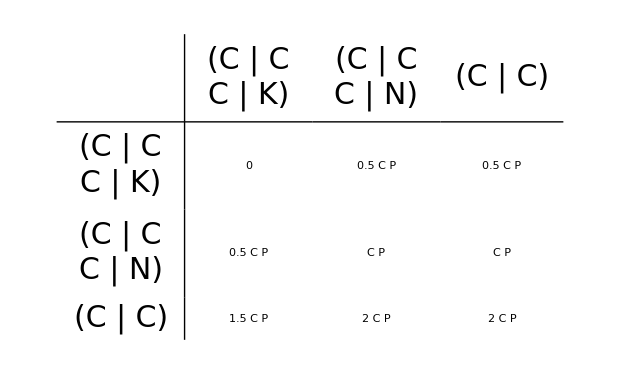
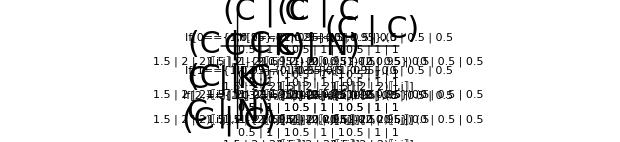

```mathematica
getStreamMatt[allplayers[[{20,23,24}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,700,(*Automatic,*){{10,10},{0,0}}]
```

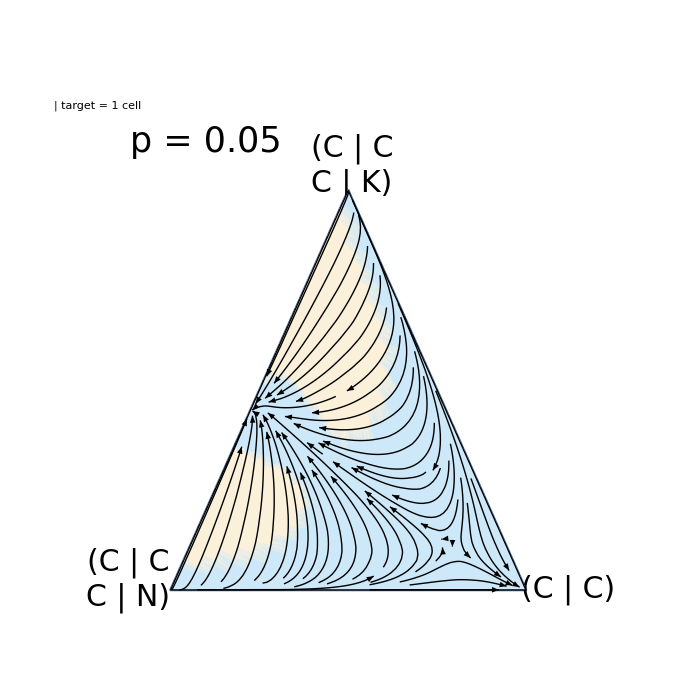
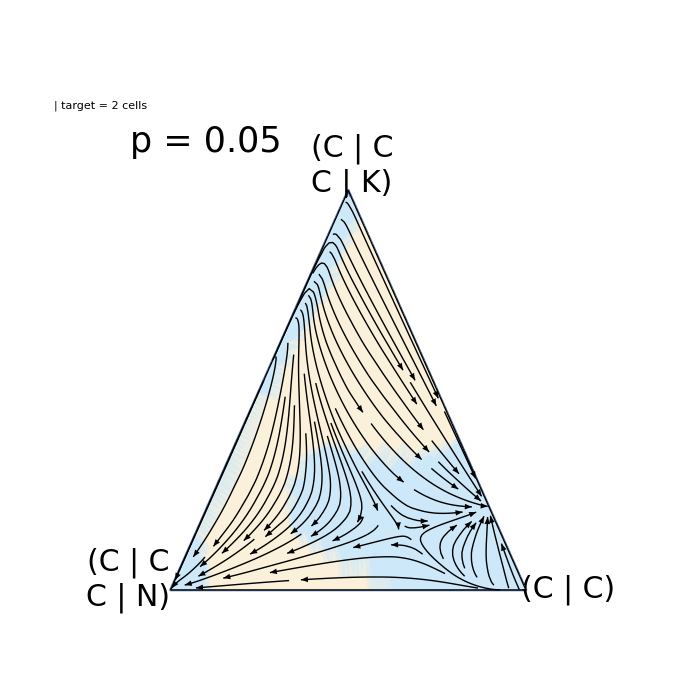
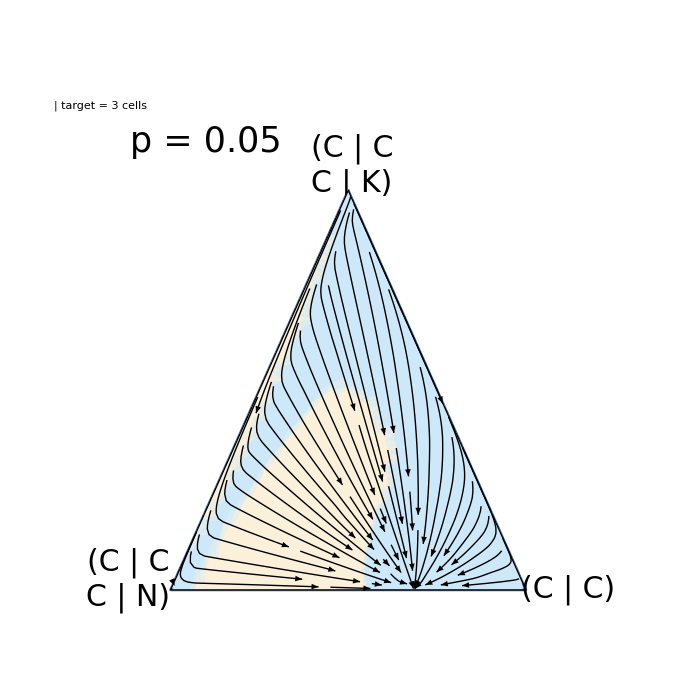
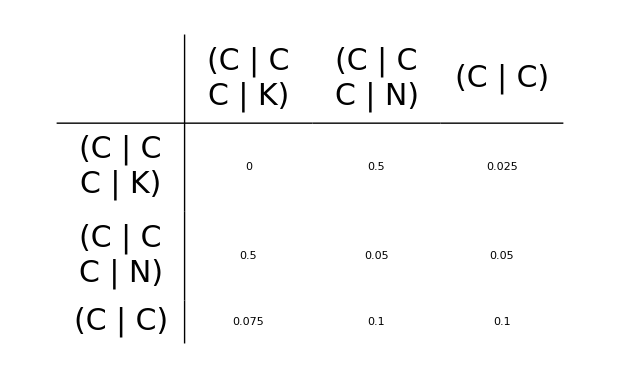
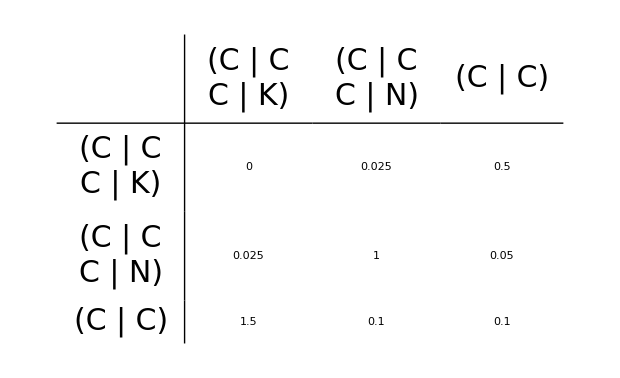
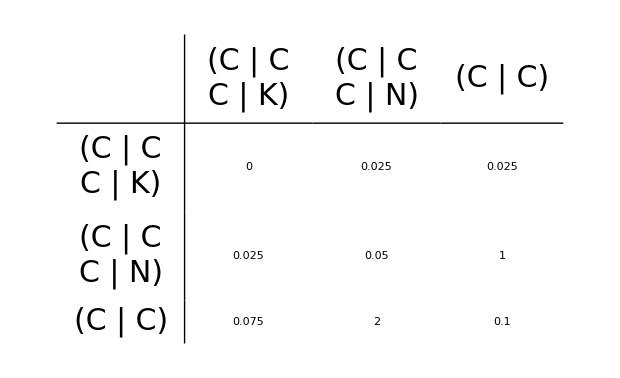
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
f4a123=getStreamPlot[allplayers[[{20,23,24}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,700,(*Automatic,*){{10,10},{0,0}},tart601]
```

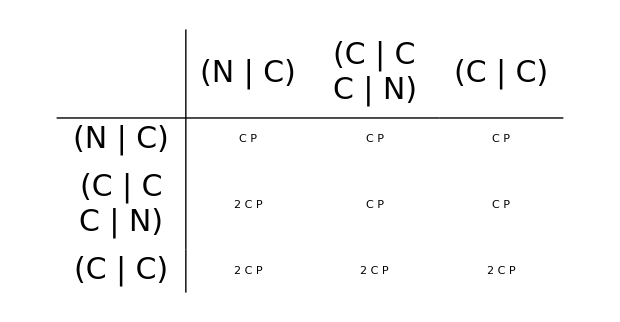
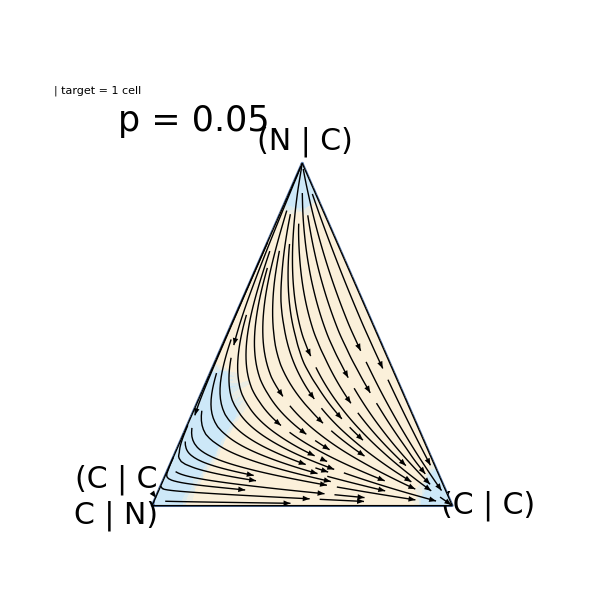
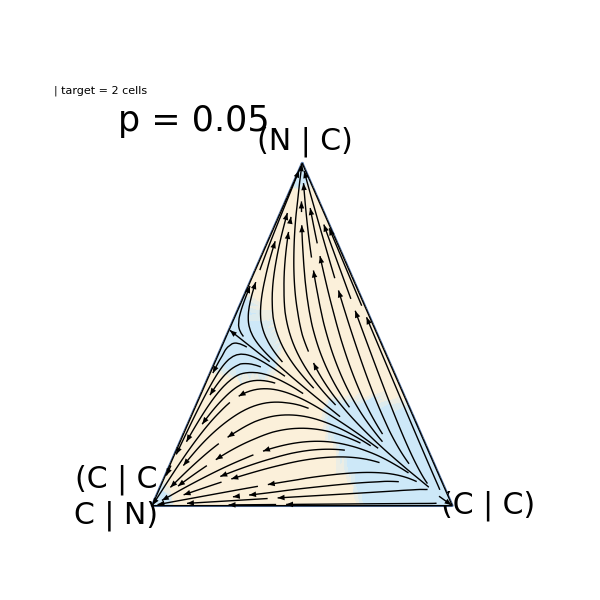
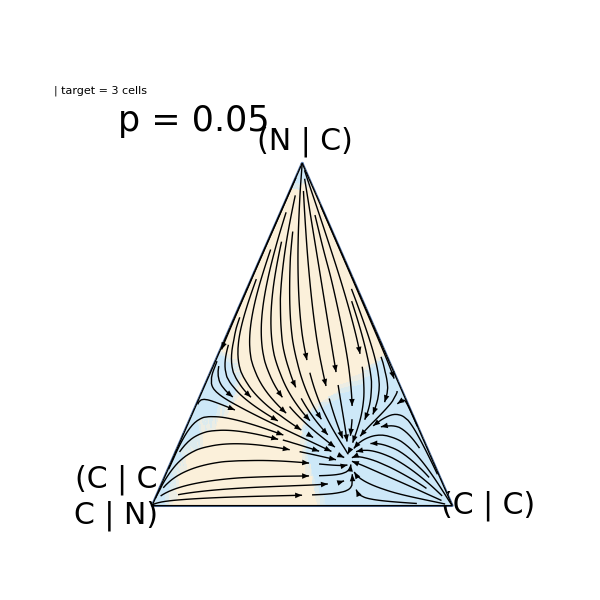
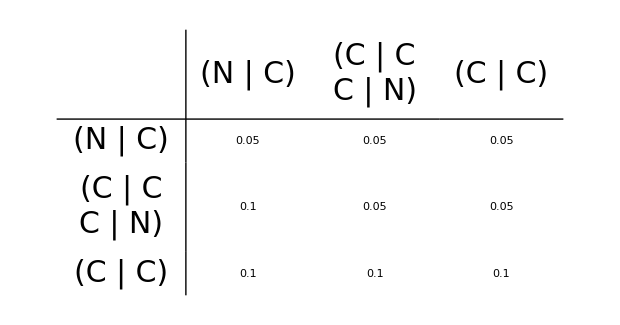
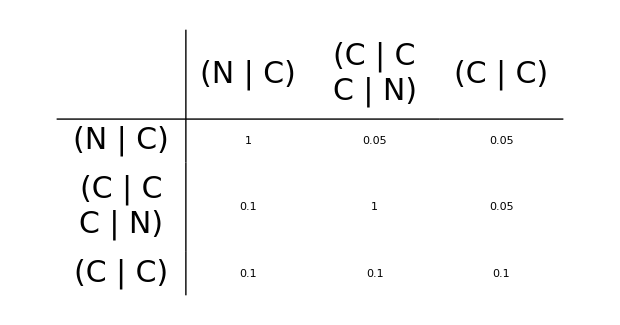
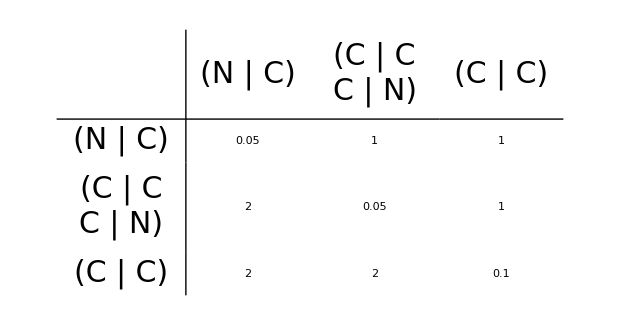

```mathematica
f4e=getStreamPlot[allplayers[[{9,23,24}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,600,(*Automatic,*){{10,10},{0,0}},tart601]
```

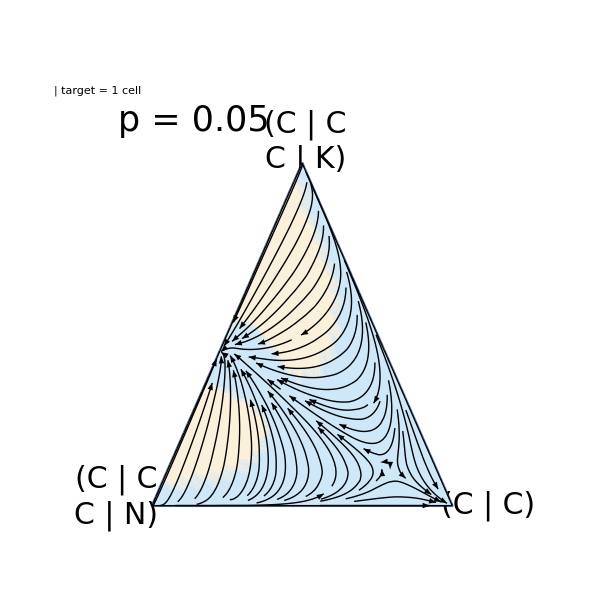
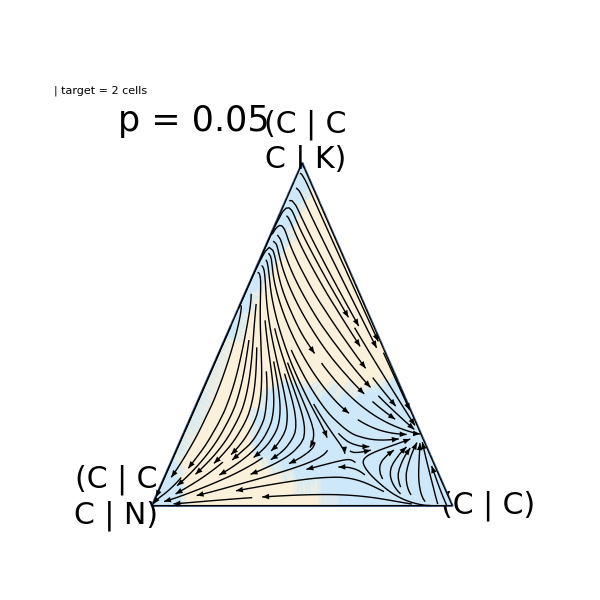
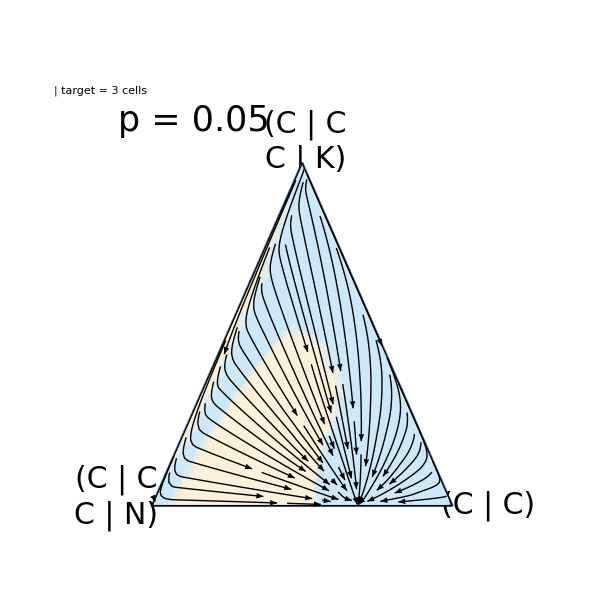
{-Graphics-,{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
f4f=getStreamPlot[allplayers[[{20,23,24}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,600,(*Automatic,*){{10,10},{0,0}},tart601]
```

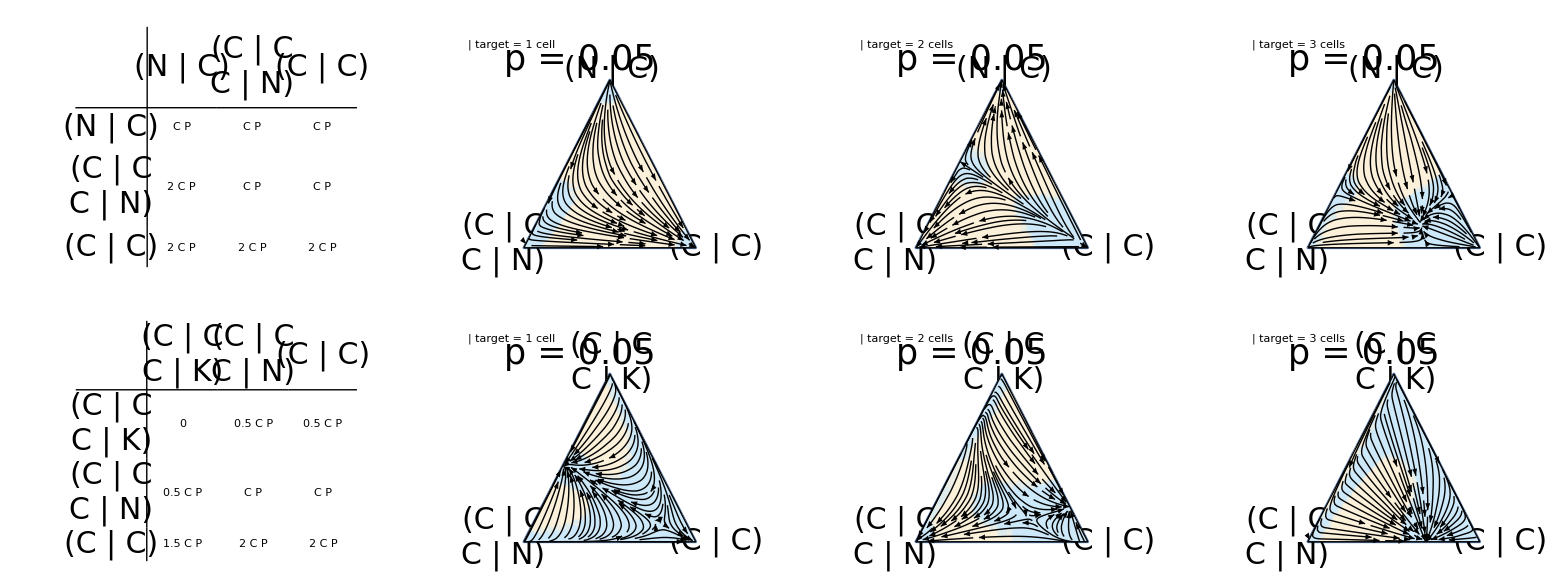

```mathematica
f4ef=TableForm[Flatten/@{f4e[[1;;2]],f4f[[1;;2]]},TableDirections->Column,TableSpacing->{30,2}]
```

```mathematica
Export[NotebookDirectory[]<>"stream_R2conditionaltarget1-3"<>ToString[{1,0.95}]<>"-2026e.png",TableForm[f4a123]]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/stream_R2conditionaltarget1-3{1, 0.95}-2026e.png

```mathematica
Export[NotebookDirectory[]<>"stream_R2conditionaltarget1-3"<>ToString[{1,0.95}]<>"-2026f.png",TableForm[f4e]]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/stream_R2conditionaltarget1-3{1, 0.95}-2026f.png

```mathematica
Export[NotebookDirectory[]<>"stream_R2conditional"<>ToString[{1,0.95}]<>"-2026-F4ef.png",f4ef(*,ImageSize->800*)]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/stream_R2conditional{1, 0.95}-2026-F4ef.png

```mathematica
"/Users/mariaabouchakra/Dropbox/Uoft/UOFT/projects/3-Evol_CellCycle/Nika/EGT_Nika/EGT_paper1_Mo/EGT_collectiverisk/streamplot/stream_R2conditional{1, 0.95}-2026-F4ef.png"
```

#### Sup

```mathematica
fS5a=getStreamPlot[allplayers[[{14,20,23}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,600,(*Automatic,*){{10,10},{0,0}},tart601];
```

```mathematica
fS5b=getStreamPlot[allplayers[[{14,20,7}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,600,(*Automatic,*){{10,10},{0,0}},tart601];
```

```mathematica
fS5c=getStreamPlot[allplayers[[{19,9,23}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,600,(*Automatic,*){{10,10},{0,0}},tart601];
```

```mathematica
fS5d=getStreamPlot[allplayers[[{20,9,23}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,600,(*Automatic,*){{10,10},{0,0}},tart601];
```

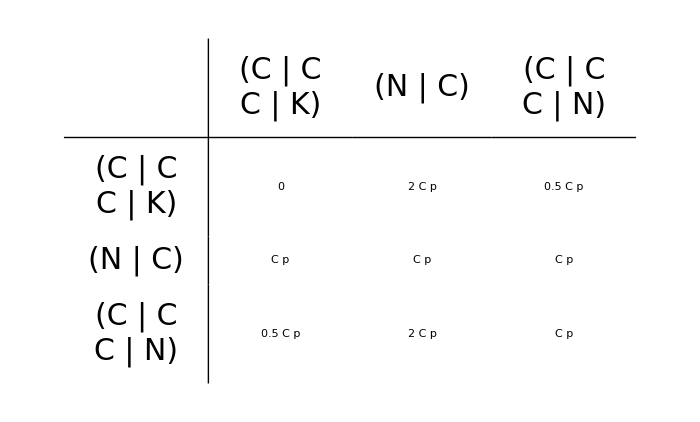

```mathematica
getStreamMatt[allplayers[[{20,9,23}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,700,vg12,700,(*Automatic,*){{10,10},{0,0}}]
```

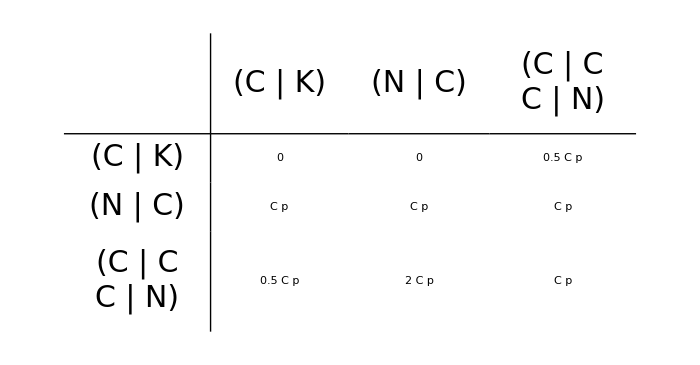

```mathematica
getStreamMatt[allplayers[[{19,9,23}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,700,vg12,700,(*Automatic,*){{10,10},{0,0}}]
```

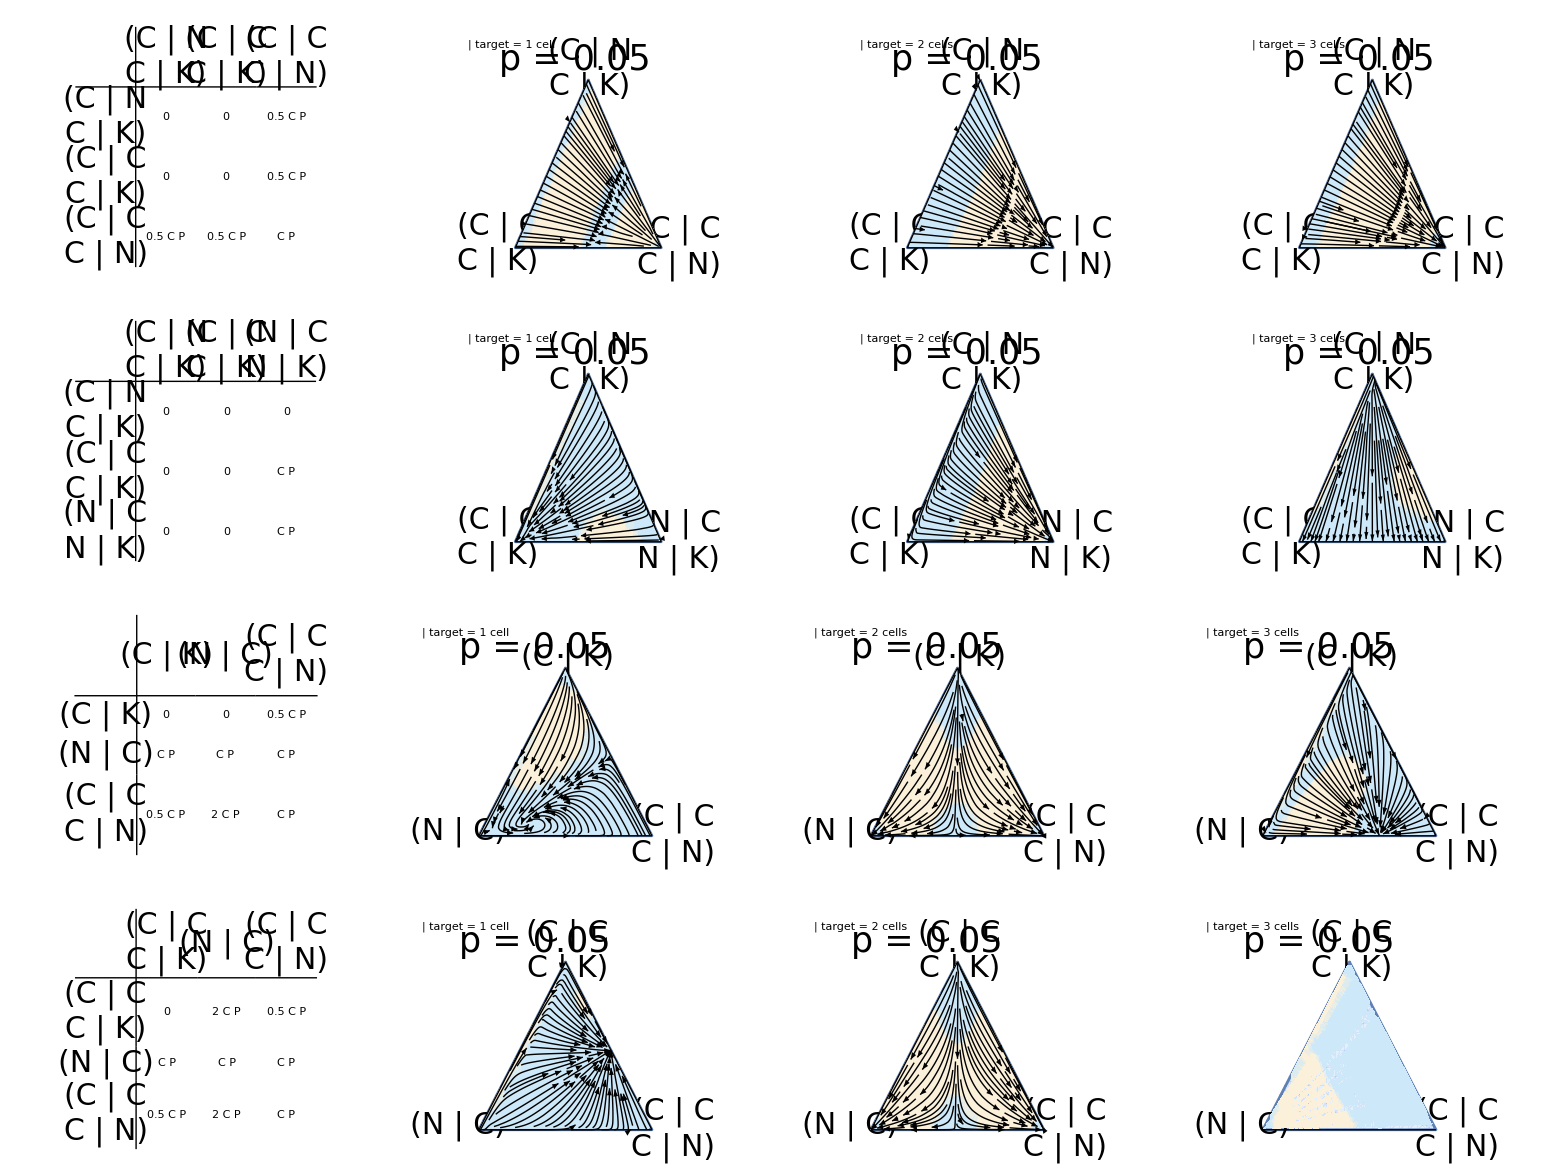

```mathematica
fS5ad=TableForm[Flatten/@{fS5a[[1;;2]],fS5b[[1;;2]],fS5c[[1;;2]],fS5d[[1;;2]]},TableDirections->Column,TableSpacing->{30,2}]
```

```mathematica
fS5e=getStreamPlot[allplayers[[{22,9,14}]],costofkilling,cond,replaceList,{{1,0.95},{2,0.95},{3,0.95}(*,{4,0.95}*)},genfont3,620,vg12,600,(*Automatic,*){{10,10},{0,0}},tart601];
```

```mathematica
Export[NotebookDirectory[]<>"stream_R2conditional"<>ToString[{1,0.95}]<>"-2026-FS13.png",fS5ad(*,ImageSize->800*)]
```

/Users/mariaabouchakra/abouchakra Dropbox/EGT/EGT_Nika/EGT_paper1_Mo/EGT_model/streamplot/stream_R2conditional{1, 0.95}-2026-FS13.png